```mathematica
naiveProjection[r_,s_]:={(2 s^4-r^2)/(8(r-s^2-2)),4((2 s^4-r^2)/(8(r-s^2-2)))+r};
(*   returns {d, y, m, z} *)
toProjectiveS[r_,s_]:=Module[{den,Z,R,S},
den=Denominator/@{r,s};
Z=LCM[den[[1]],den[[2]]];
R=r*Z;
S=s*Z;
Return[{(R^3*S-3*R^2*S^2+5*R*S^3-3*S^4+R^2*S*Z-3*R*S^2*Z+2*S^3*Z),
R^4-4*R^3*S+6*R^2*S^2-4*R*S^3+S^4+R^3*Z-4*R^2*S*Z+7*R*S^2*Z-6*S^3*Z+1/2*R^2*Z^2-2*R*S*Z^2+2*S^2*Z^2,
-1/4*R^4+R^3*S-3/2*R^2*S^2+R*S^3-1/4*S^4+1/8*R^2*Z^2-1/2*R*S*Z^2+1/2*S^2*Z^2,
R^2*S^2-2*R*S^3+3*S^4+R*S^2*Z-2*S^3*Z}];
]
(*   returns {m, d, y}  *)
Mmap[r_,s_]:=Module[{d,y,m,z},
{d,y,m,z}=toProjectiveS[r,s];
Return[{m/z,d/z, y/z}];
]
gammaplus[m_,d_,y_]:=y(-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
gammaminus[m_,d_,y_]:=-y(-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
(* given rational (r,s=d) in A^2, returns (m,y) that is a solution to S *)
ϕ[r_,s_]:={(-4-4 r-r^2-4 s^2-2 r s^2+s^4)/(8 r),(-4+r^2-4 s^2+s^4)/(2 r)};
(* given m and d, return gamma *)
gamma[m_,d_]:=Sign[d] Sqrt[2 d^4+8m d^2+16 m^2+16m](-3/16 d^6-m/2 d^4-m^2/2 d^2-m/2 d^2)+17/64 d^8+(5m)/4 d^6+(11 m^2)/4 d^4+(7m)/4 d^4+2 m^3 d^2+2 m^2 d^2-m;
```

```mathematica
{m,y}=naiveProjection[r,s];
-m-gammaplus[m,s,y]//FullSimplify
m^2+m+gammaplus[m,s,y]//FullSimplify
```

((2 r-3 s^2) ((-4+r) r s-4 (-1+r) s^3+4 s^5)^2)/(256 (2-r+s^2)^2)

-((r-2 s^2)^2 (-4 r^2+2 r (8+(-8+r) r) s^2+(-16+(40-11 r) r) s^4+4 (-6+5 r) s^6-12 s^8))/(256 (2-r+s^2)^2)

```mathematica
(2 r-3 s^2)
-(-4 r^2+2 r (8+(-8+r) r) s^2+(-16+(40-11 r) r) s^4+4 (-6+5 r) s^6-12 s^8)//Expand
```

2 r-3 s^2

4 r^2-16 r s^2+16 r^2 s^2-2 r^3 s^2+16 s^4-40 r s^4+11 r^2 s^4+24 s^6-20 r s^6+12 s^8

```mathematica
(* for any s, as r gets big enough the second expression is negative. For r = 1 or 3 mod 4, 2r-3 s^2 is not a square (show mod 4). So just choose r to be big enough and 1 or 3 mod 4. *)
```

```mathematica
{m,y}=ϕ[r,s];
-m-gammaplus[m,s,y]//FullSimplify
m^2+m+gammaplus[m,s,y]//FullSimplify
```

(s^2 (4+2 r-s^2) (-4+r^2-2 (2+r) s^2+s^4)^2)/(256 r^2)

-((2+r-s^2)^2 (-4 (2+r)^2+2 (2+r) (-8+(-4+r) r) s^2-(8+r (12+5 r)) s^4+4 (2+r) s^6-s^8))/(256 r^2)

```mathematica
4+2 r-s^2
-(-4 (2+r)^2+2 (2+r) (-8+(-4+r) r) s^2-(8+r (12+5 r)) s^4+4 (2+r) s^6-s^8)//Expand
```

4+2 r-s^2

16+16 r+4 r^2+32 s^2+32 r s^2+4 r^2 s^2-2 r^3 s^2+8 s^4+12 r s^4+5 r^2 s^4-8 s^6-4 r s^6+s^8

```mathematica
n=5;
Print[Mod[#^2,n]&/@Range[0,n-1]];
Do[
r=t[[1]];
s=t[[2]];
Print[{{r,s},Mod[4+2 r-s^2,n]}];
,{t,Tuples[Range[0,n-1],2]}]
```

{0,1,4,4,1}

{{0,0},4}

{{0,1},3}

{{0,2},0}

{{0,3},0}

{{0,4},3}

{{1,0},1}

{{1,1},0}

{{1,2},2}

{{1,3},2}

{{1,4},0}

{{2,0},3}

{{2,1},2}

{{2,2},4}

{{2,3},4}

{{2,4},2}

{{3,0},0}

{{3,1},4}

{{3,2},1}

{{3,3},1}

{{3,4},4}

{{4,0},2}

{{4,1},1}

{{4,2},3}

{{4,3},3}

{{4,4},1}

```mathematica
Refine[Max[Solve[16+16 r+4 r^2+32 s^2+32 r s^2+4 r^2 s^2-2 r^3 s^2+8 s^4+12 r s^4+5 r^2 s^4-8 s^6-4 r s^6+s^8==0,r][[All,1,2]]], {s>0}]
```

Max[(4+4 s^2+5 s^4)/(6 s^2)+(-16-128 s^2-248 s^4-112 s^6-s^8)/(6 s^2 (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))-((-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))/(6 s^2),(4+4 s^2+5 s^4)/(6 s^2)-((1+ⅈ √3) (-16-128 s^2-248 s^4-112 s^6-s^8))/(12 s^2 (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))+((1-ⅈ √3) (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))/(12 s^2),(4+4 s^2+5 s^4)/(6 s^2)-((1-ⅈ √3) (-16-128 s^2-248 s^4-112 s^6-s^8))/(12 s^2 (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))+((1+ⅈ √3) (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))/(12 s^2)]

```mathematica
Clear[r,s]
```

```mathematica
Slider[Dynamic[s],{-20,20}]
Dynamic[
z=Solve[16+16 r+4 r^2+32 s^2+32 r s^2+4 r^2 s^2-2 r^3 s^2+8 s^4+12 r s^4+5 r^2 s^4-8 s^6-4 r s^6+s^8==0,r][[3,1,2]];
zzz=(4+4 s^2+5 s^4)/(6 s^2)-((1+ⅈ √3) (-16-128 s^2-248 s^4-112 s^6-s^8))/(12 s^2 (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))+((1-ⅈ √3) (-64-768 s^2-3024 s^4-4576 s^6-2700 s^8-264 s^10+s^12+12 √6 √(64 s^10+480 s^12+720 s^14+112 s^16-180 s^18+30 s^20-s^22))^(1/3))/(12 s^2);
Show[
Plot[16+16 r+4 r^2+32 s^2+32 r s^2+4 r^2 s^2-2 r^3 s^2+8 s^4+12 r s^4+5 r^2 s^4-8 s^6-4 r s^6+s^8,{r,0,z+20}],
ListPlot[{{zzz,0}},PlotStyle->PointSize[0.03]]
]
]
```

```mathematica
z
```

33.339

```mathematica
vmax=20;
msgammas={Join[{""},Table["u="<>ToString[s],{s,0,2}]]};
Do[
AppendTo[msgammas,{"v="<>ToString[v]}];
Do[
s=2v;
If[s≠0,
r=2Ceiling[FindRoot[16+16 r+4 r^2+32 s^2+32 r s^2+4 r^2 s^2-2 r^3 s^2+8 s^4+12 r s^4+5 r^2 s^4-8 s^6-4 r s^6+s^8==0,{r,0}][[1,2]]/2]+2u+1;
{m,y}=ϕ[r,s];
γ=gamma[m,s];
AppendTo[msgammas[[Length[msgammas]]],{m,γ}];
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[f[f[x]]]]||¬IrreduciblePolynomialQ[f[f[x]]],
Print["uh-oh",{u,v}];
]
]
,{u,0,10}],{v,-vmax,vmax}]
TableForm[msgammas,TableDepth->2]
```

FindRoot::lstol: The line search decreased the step size to within tolerance specified by AccuracyGoal and PrecisionGoal but was unable to find a sufficient decrease in the merit function. You may need more than MachinePrecision digits of working precision to meet these tolerances.

General::stop: Further output of FindRoot::lstol will be suppressed during this calculation.

| u=0 | u=1 | u=2 |  |  |  |  |  |  |  | 
v=-20 | {-654409/6408,10587029050086225223409/4111379208} | {-664025/6424,10627697734413675271225/4142253016} | {-673649/6440,426739612787504699833/166931240} | {-683281/6456,10709407086158938022969/4204463544} | {-692921/6472,10750448314496036425201/4235801032} | {-702569/6488,10791614285785132153849/4267293848} | {-712225/6504,10832905281530570971025/4298942376} | {-721889/6520,86994572669241051053/34645976} | {-731561/6536,10915863474500331065329/4362708104} | {-741241/6552,10957531236826733308601/4394826072} | {-750929/6568,10999325153814253436689/4427101288}
v=-19 | {-534289/5784,1290364504683752228705/755866134} | {-542969/5800,1295858009618996937961/762156250} | {-551657/5816,1301370061174894053793/768481166} | {-560353/5832,1306900705833967915193/774840978} | {-569057/5848,1312449990155464972513/781235782} | {-577769/5864,1318017960775416168265/787665674} | {-586489/5880,1323604664406699317921/794130750} | {-595217/5896,1329210147839101490713/800631106} | {-603953/5912,1334834457939381390433/807166838} | {-612697/5928,3713234464408121153/2254122} | {-621449/5944,1346139745995841643425/820344814}
v=-18 | {-431577/5192,2420372276186980689675/2186875592} | {-62767/744,787773361572983329/714984} | {-447169/5224,2443383662793402337795/2227560616} | {-454977/5240,2454954283686946076487/2248091000} | {-462793/5256,10150487040022372249/9336408} | {-470617/5272,2478225984999928834015/2289529432} | {-478449/5288,2489927307823729149363/2310438248} | {-486289/5304,277963604525843873215/259052664} | {-70591/760,7327876109285527309/6859000} | {-501993/5336,2525294624062015457487/2373927704} | {-509857/5352,281907990963127913995/266149608}
v=-17 | {-344497/4632,135856021885979848960/194104539} | {-50207/664,398189268753128957/571787} | {-358409/4664,137304865944775748390/198155287} | {-365377/4680,138033871720128823849/200201625} | {-372353/4696,138765946074851913644/202262003} | {-379337/4712,139501098595112477015/204336469} | {-386329/4728,140239338886795953106/206425071} | {-393329/4744,140980676575525736645/208527857} | {-57191/680,1429732780238312/2125} | {-2047/24,18078915415621/27} | {-414377/4792,143223370576715702270/214921799}
v=-16 | {-271369/4104,464884517651650165385/1080045576} | {-277529/4120,467678110332155300449/1092727000} | {-283697/4136,470485009008585049417/1105507304} | {-289873/4152,473305260706983083777/1118386872} | {-296057/4168,476138912562800168137/1131366088} | {-302249/4184,478986011821019497825/1144445336} | {-308449/4200,481846605836282036489/1157625000} | {-314657/4216,484720742073011853697/1170905464} | {-13951/184,40076310356336111/97336} | {-327097/4248,490509831618237157217/1197770328} | {-333329/4264,493424880405624350665/1211355496}
v=-15 | {-210609/3608,23528212340299730748/91733851} | {-216025/3624,877375963102897725/3442951} | {-221449/3640,190807696249574266/753571} | {-226881/3656,24013648930442809293/95443993} | {-232321/3672,2686357246520825608/10744731} | {-237769/3688,24341664422397525803/97972181} | {-243225/3704,24507000077347835550/99252847} | {-248689/3720,36552927005382307/148955} | {-254161/3736,24840344930679941588/101847563} | {-259641/3752,25008361247259388647/103161709} | {-265129/3768,932491787092538654/3869893}
v=-14 | {-160729/3144,71593051576603091915/485587656} | {-165449/3160,72155533195835002159/493039000} | {-170177/3176,72721515788734266307/500566184} | {-174913/3192,1495735010532414263/10370808} | {-179657/3208,73864048587769926907/515849608} | {-184409/3224,74440631262810772255/523606616} | {-189169/3240,75020779849474634099/531441000} | {-193937/3256,75604510705330871287/539353144} | {-198713/3272,76191840237327784747/547343432} | {-203497/3288,76782784901865999887/555412248} | {-208289/3304,225589974358226965/1643032}
v=-13 | {-120337/2712,6336137328234541385/77916438} | {-124409/2728,6393910795953466657/79303642} | {-128489/2744,6452101443205979305/80707214} | {-132577/2760,6510711503384772113/82127250} | {-136673/2776,6569743217747332873/83563846} | {-140777/2792,6629198835429572545/85017098} | {-144889/2808,39580358659523393/511758} | {-149009/2824,6749390816770617265/87973954} | {-153137/2840,6810131718216013513/89477750} | {-157273/2856,6871305598581527393/90998586} | {-161417/2872,6932914746599608105/92536558}
v=-12 | {-88137/2312,8254852360401482865/193100552} | {-91609/2328,309009795952977339/7301384} | {-95089/2344,8432426192306803345/201230056} | {-98577/2360,8522342174664942777/205379000} | {-102073/2376,957001907421660713/23287176} | {-105577/2392,8704455917182416505/213847192} | {-109089/2408,8796663193847954193/218167208} | {-112609/2424,329246066088396155/8242408} | {-116137/2440,8983402496007851377/226981000} | {-119673/2456,9077944155574237497/231475544} | {-123217/2472,339750874431178435/8741816}
v=-11 | {-62929/1944,609478460242968035/28697814} | {-9407/280,1799578984828297/85750} | {-68777/1976,625111234581020683/30138446} | {-71713/1992,633045975643775303/30876498} | {-74657/2008,641060404915138483/31626502} | {-77609/2024,5364918307583095/267674} | {-80569/2040,657330702272112731/33162750} | {-83537/2056,665587764705517303/33949186} | {-12359/296,1964801469554101/101306} | {-89497/2088,682348724785573103/35559162} | {-92489/2104,690853834276432555/36382894}
v=-10 | {-43609/1608,640711667198080859/64964808} | {-6575/232,1896847444360825/195112} | {-48449/1640,5285174245417679/551368} | {-50881/1656,670797084630513719/70957944} | {-53321/1672,681070687433968651/73034632} | {-55769/1688,691468697775078799/75151448} | {-58225/1704,701992230889566275/77308776} | {-60689/1720,28505696343215167/3180280} | {-9023/248,2109097257249853/238328} | {-65641/1752,734327217852951551/84027672} | {-68129/1768,745364126047809139/86350888}
v=-9 | {-29169/1304,18272763087805395/4330747} | {-31129/1320,2069141106969092/499125} | {-33097/1336,18977056325961749/4657463} | {-35073/1352,19337181146848494/4826809} | {-37057/1368,81081085707373/20577} | {-39049/1384,20073684201342200/5177717} | {-41049/1400,20450182540747833/5359375} | {-43057/1416,2314695505834226/616137} | {-45073/1432,21219976382429339/5735339} | {-47097/1448,21613394616280524/5929741} | {-49129/1464,2445841809038645/680943}
v=-8 | {-18697/1032,27997868564072105/17173512} | {-20249/1048,28677511162727233/17984728} | {-21809/1064,29370164513856745/18821096} | {-23377/1080,30076012540261217/19683000} | {-24953/1096,30795240868607977/20570824} | {-26537/1112,31528036837172545/21484952} | {-28129/1128,32274589503580073/22425768} | {-29729/1144,33035089652546785/23393656} | {-31337/1160,33809729803621417/24389000} | {-32953/1176,34598704218926657/25412184} | {-34577/1192,35402208910900585/26463592}
v=-7 | {-11377/792,536721832752625/970299} | {-12569/808,553807840602206/1030301} | {-13769/824,571321896295115/1092727} | {-14977/840,12025957203136/23625} | {-16193/856,607665859151429/1225043} | {-17417/872,626511859477730/1295029} | {-18649/888,645818095102111/1367631} | {-19889/904,665592854338820/1442897} | {-919/40,56369238367/125} | {-22393/936,706581586016614/1601613} | {-23657/952,14853318895715/34391}
v=-6 | {-6489/584,491873058276795/3112136} | {-7369/600,19011812349997/125000} | {-8257/616,535498292111347/3652264} | {-9153/632,558429566165847/3944312} | {-10057/648,64681276629203/472392} | {-10969/664,606623101215535/4574296} | {-11889/680,631923746420259/4913000} | {-12817/696,24372336306501/195112} | {-13753/712,685031069601307/5639752} | {-14697/728,712877995458207/6028568} | {-15649/744,27467202058025/238328}
v=-5 | {-3409/408,9439969146071/265302} | {-4025/424,10038834863275/297754} | {-4649/440,426693658087/13310} | {-5281/456,11326561396211/370386} | {-5921/472,12017592376519/410758} | {-6569/488,12741557559931/453962} | {-7225/504,13499605886975/500094} | {-7889/520,114343298879/4394} | {-8561/536,15122678330551/601526} | {-9241/552,15990131788619/657018} | {-9929/568,16896527649391/715822}
v=-4 | {-1609/264,1615827648305/287496} | {-287/40,5186898223/1000} | {-2417/296,1955127056977/405224} | {-2833/312,2144610772217/474552} | {-3257/328,2348303674417/551368} | {-3689/344,2566978876345/636056} | {-4129/360,2801436626129/729000} | {-4577/376,3052504768057/830584} | {-719/56,9682330039/2744} | {-5497/408,3607924351097/1061208} | {-5969/424,3914073608785/1191016}
v=-3 | {-657/152,6760404405/13718} | {-127/24,866777/2} | {-1129/184,9473254405/24334} | {-1377/200,11116496133/31250} | {-1633/216,1441787117/4374} | {-1897/232,15072332965/48778} | {-2169/248,17426769957/59582} | {-2449/264,743043295/2662} | {-391/40,67062931/250} | {-3033/296,26273390373/101306} | {-3337/312,1107455775/4394}
v=-2 | {-217/72,75097835/5832} | {-329/88,111017743/10648} | {-449/104,159018595/17576} | {-577/120,221820647/27000} | {-713/136,302513947/39304} | {-857/152,404581375/54872} | {-1009/168,531921683/74088} | {-1169/184,688872535/97336} | {-1337/200,880233547/125000} | {-1513/216,1111289327/157464} | {-1697/232,1387832515/195112}
v=-1 | {-17/8,-53/32} | {-49/24,-50/27} | {-89/40,-187/125} | {-137/56,-436/343} | {-193/72,-821/729} | {-257/88,-1366/1331} | {-329/104,-2095/2197} | {-409/120,-3032/3375} | {-497/136,-4201/4913} | {-593/152,-5626/6859} | {-697/168,-7331/9261}
v=0 |  |  |  |  |  |  |  |  |  |  | 
v=1 | {-17/8,-1} | {-49/24,-55/32} | {-89/40,-1/32} | {-137/56,61/32} | {-193/72,83/32} | {-257/88,17/32} | {-329/104,-185/32} | {-409/120,-571/32} | {-497/136,-1189/32} | {-593/152,-2087/32} | {-697/168,-3313/32}
v=2 | {-217/72,145/108} | {-329/88,-2813/484} | {-449/104,-9265/676} | {-577/120,-5291/300} | {-713/136,-18629/1156} | {-857/152,-14485/1444} | {-1009/168,-1091/588} | {-1169/184,10375/2116} | {-1337/200,15107/2500} | {-1513/216,-3023/972} | {-1697/232,-92705/3364}
v=3 | {-657/152,-486855/11552} | {-127/24,-1307/96} | {-1129/184,76085/16928} | {-1377/200,78651/20000} | {-1633/216,-29783/2592} | {-1897/232,-926665/26912} | {-2169/248,-1773459/30752} | {-2449/264,-877615/11616} | {-391/40,-67591/800} | {-3033/296,-3635217/43808} | {-3337/312,-1159625/16224}
v=4 | {-1609/264,-1947905/2904} | {-287/40,-27269/40} | {-2417/296,-6069479/10952} | {-2833/312,-1561871/4056} | {-3257/328,-3050347/13448} | {-3689/344,-1544945/14792} | {-4129/360,-28417/1080} | {-4577/376,157931/17672} | {-719/56,3133/392} | {-5497/408,-138419/6936} | {-5969/424,-1461175/22472}
v=5 | {-3409/408,-99468413/27744} | {-4025/424,-406399825/89888} | {-4649/440,-91762879/19360} | {-5281/456,-156200519/34656} | {-5921/472,-447053119/111392} | {-6569/488,-403896089/119072} | {-7225/504,-115796225/42336} | {-7889/520,-56883257/27040} | {-8561/536,-220587527/143648} | {-9241/552,-53443403/50784} | {-9929/568,-106987339/161312}
v=6 | {-6489/584,-268420185/21316} | {-7369/600,-26202719/1500} | {-8257/616,-68715851/3388} | {-9153/632,-537722469/24964} | {-10057/648,-63124009/2916} | {-10969/664,-576698825/27556} | {-11889/680,-113512257/5780} | {-12817/696,-181464959/10092} | {-13753/712,-510509129/31684} | {-14697/728,-66978423/4732} | {-15649/744,-140670655/11532}
v=7 | {-11377/792,-3640258645/104544} | {-12569/808,-16617723529/326432} | {-13769/824,-21190122275/339488} | {-14977/840,-1178746489/16800} | {-16193/856,-27417221767/366368} | {-17417/872,-29282915345/380192} | {-18649/888,-10148807353/131424} | {-19889/904,-30997103605/408608} | {-919/40,-58635551/800} | {-22393/936,-10195683379/146016} | {-23657/952,-4253602165/64736}
v=8 | {-18697/1032,-1215946415/14792} | {-20249/1048,-17043140101/137288} | {-21809/1064,-3180996845/20216} | {-23377/1080,-2964669649/16200} | {-24953/1096,-30352302703/150152} | {-26537/1112,-33338902925/154568} | {-28129/1128,-3966674219/17672} | {-29729/1144,-37491242785/163592} | {-31337/1160,-38765138231/168200} | {-32953/1176,-628123691/2744} | {-34577/1192,-39958632715/177608}
v=9 | {-29169/1304,-147286036575/850208} | {-31129/1320,-15526016071/58080} | {-33097/1336,-309092570371/892448} | {-35073/1352,-376450571277/913952} | {-37057/1368,-48389163887/103968} | {-39049/1384,-486767508145/957728} | {-41049/1400,-106149240783/196000} | {-43057/1416,-189306904327/334176} | {-45073/1432,-598755114607/1025312} | {-47097/1448,-623695727673/1048352} | {-49129/1464,-214390473905/357216}
v=10 | {-43609/1608,-6015229737/17956} | {-6575/232,-1765481225/3364} | {-48449/1640,-23212568513/33620} | {-50881/1656,-15881490181/19044} | {-53321/1672,-15204557563/15884} | {-55769/1688,-189139190833/178084} | {-58225/1704,-23191461525/20164} | {-60689/1720,-45224204929/36980} | {-9023/248,-4927516081/3844} | {-65641/1752,-28312995297/21316} | {-68129/1768,-266335625333/195364}
v=11 | {-62929/1944,-381348848605/629856} | {-9407/280,-7518880973/7840} | {-68777/1976,-2490776469851/1952288} | {-71713/1992,-1030638905959/661344} | {-74657/2008,-3647421137503/2016032} | {-77609/2024,-378101911435/186208} | {-80569/2040,-308586992429/138720} | {-83537/2056,-5058218894461/2113568} | {-12359/296,-111205456343/43808} | {-89497/2088,-1934337732331/726624} | {-92489/2104,-6121678379755/2213408}
v=12 | {-88137/2312,-692229010275/668168} | {-91609/2328,-373664687267/225816} | {-95089/2344,-1524542897095/686792} | {-98577/2360,-1903692020301/696200} | {-102073/2376,-22820630137/7128} | {-105577/2392,-199383040405/55016} | {-109089/2408,-2902673708271/724808} | {-112609/2424,-1064026686055/244824} | {-116137/2440,-3460938701491/744200} | {-119673/2456,-3709974903993/753992} | {-123217/2472,-1313299736285/254616}
v=13 | {-120337/2712,-2076982870925/1225824} | {-124409/2728,-10134737735329/3720992} | {-128489/2744,-1977803576765/537824} | {-132577/2760,-5788643764343/1269600} | {-136673/2776,-20703891289327/3853088} | {-140777/2792,-23863654474985/3897632} | {-144889/2808,-688468861781/101088} | {-149009/2824,-29668765411885/3987488} | {-153137/2840,-32323991210039/4032800} | {-157273/2856,-1658132266157/194208} | {-161417/2872,-37163857041595/4124192}
v=14 | {-160729/3144,-549337465735/205932} | {-165449/3160,-537954879409/124820} | {-170177/3176,-3687227134297/630436} | {-174913/3192,-221019739189/30324} | {-179657/3208,-5553365979341/643204} | {-184409/3224,-494161270465/49972} | {-189169/3240,-483640455743/43740} | {-193937/3256,-8045883427217/662596} | {-198713/3272,-8798898655429/669124} | {-203497/3288,-3171536953207/225228} | {-208289/3304,-1456280635055/97468}
v=15 | {-210609/3608,-26461518167439/6508832} | {-216025/3624,-14436020280275/2188896} | {-221449/3640,-1700967120497/189280} | {-226881/3656,-75151579712157/6683168} | {-232321/3672,-10019310616991/749088} | {-237769/3688,-104612887644289/6800672} | {-243225/3704,-118481095431675/6859808} | {-248689/3720,-8786033851019/461280} | {-254161/3736,-144553063764127/6978848} | {-259641/3752,-22397221954287/1005536} | {-265129/3768,-56161539920513/2366304}
v=16 | {-271369/4104,-4227780440125/701784} | {-277529/4120,-4160951277617/424360} | {-283697/4136,-28664325405899/2138312} | {-289873/4152,-12088914131971/718296} | {-296057/4168,-43616651712127/2171528} | {-302249/4184,-50718648286205/2188232} | {-308449/4200,-3838485191549/147000} | {-314657/4216,-3776296311617/130696} | {-13951/184,-133426039127/4232} | {-327097/4248,-25579229925079/751896} | {-333329/4264,-82667334035035/2272712}
v=17 | {-344497/4632,-10382867005335/1191968} | {-50207/664,-3133983200521/220448} | {-358409/4664,-211973832752435/10876448} | {-365377/4680,-29855430490421/1216800} | {-372353/4696,-323767151814487/11026208} | {-379337/4712,-377205262489025/11101472} | {-386329/4728,-47671061401251/1241888} | {-393329/4744,-479296118104165/11252768} | {-57191/680,-633854508703/13600} | {-2047/24,-1613817873/32} | {-414377/4792,-620856695578435/11481632}
v=18 | {-431577/5192,-20766266127045/1684804} | {-62767/744,-232511787079/11532} | {-447169/5224,-47252796007625/1705636} | {-454977/5240,-59991743330793/1716100} | {-462793/5256,-8044535784661/191844} | {-470617/5272,-84484739857565/1737124} | {-478449/5288,-96248164794273/1747684} | {-486289/5304,-2111680892635/34476} | {-70591/760,-127639110023/1900} | {-501993/5336,-129661572785589/1779556} | {-509857/5352,-46729640299795/596748}
v=19 | {-534289/5784,-31798959958895/1858592} | {-542969/5800,-94331156406701/3364000} | {-551657/5816,-652919701549931/16912928} | {-560353/5832,-92226166382653/1889568} | {-569057/5848,-1003055872376623/17099552} | {-577769/5864,-1172033133792425/17193248} | {-586489/5880,-29711537673439/384160} | {-595217/5896,-1498065578082541/17381408} | {-603953/5912,-1655223412236407/17475872} | {-612697/5928,-10576277416403/102752} | {-621449/5944,-1958076008140795/17665568}
v=20 | {-654409/6408,-39941846073697/1710936} | {-664025/6424,-197697330800425/5158472} | {-673649/6440,-7828017218893/148120} | {-683281/6456,-116231149604911/1736664} | {-692921/6472,-421853842428811/5235848} | {-702569/6488,-493479635212241/5261768} | {-712225/6504,-187862852599525/1762584} | {-721889/6520,-126439644026033/1062760} | {-731561/6536,-36806637465377/281048} | {-741241/6552,-36428076316501/255528} | {-750929/6568,-829205942715991/5392328}

```mathematica
max=1000;
times=Table[{2^i},{i,0,max}];
Do[
n=2^i;
AppendTo[times[[i+1]],Timing[IrreduciblePolynomialQ[x^8+17 n/42069 x^7-1800/n x^5+24n x^4+x^3-797n x-n]][[1]]];
,{i,0,max}]
```

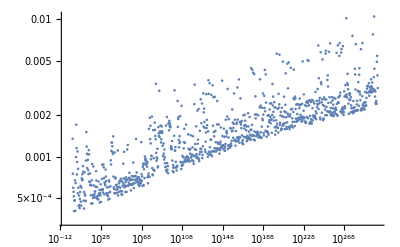

```mathematica
ListLogLogPlot[times]
```

```mathematica
(* inverse of magma map: from homogeneous curve S (d,y,m,z) to P^2 (R,S,Z)  *)
```

```mathematica
R=d^2-z^2
S=d*z-z^2
Z=y*z+4*m*z
```

```mathematica
(* takes a point on S (m,d,y) to A^2 (r,s) *)
Minverse[m_,d_,y_]:=Module[{denoms,mm,yy,dd,zz,R,S,Z},
denoms=Denominator@{m,y,d};
zz=LCM[denoms[[1]],denoms[[2]],denoms[[3]]];
mm=m*zz; (* to projective S *)
yy=y*zz;
dd=d*zz;
R=dd^2-zz^2; (* to P^2 *)
S=dd*zz-zz^2;
Z=yy*zz+4*mm*zz;
Return[{R/Z,S/Z}](* to A^2 *)
]
```

```mathematica
(* verifying that they're actually inverses *)
sol=Mmap[r,s];
Minverse[sol[[1]],sol[[2]],sol[[3]]]//FullSimplify
```

{r,s}

```mathematica
Clear[m,d,y]
```

```mathematica
sol=Minverse[m,d,y];
Mmap[sol[[1]],sol[[2]]]//FullSimplify
```

{(-2 d^4+(4 m+y)^2)/(8 (2+d^2+4 m+y)),d,(2 d^4+2 d^2 (4 m+y)+(4 m+y) (4+4 m+y))/(2 (2+d^2+4 m+y))}

```mathematica
(* returns the (r,s) that will map to Subscript[f, m,γ] using Magma's map. Note, the result is only meaningful if m,γ actually result from a point on S, specifically f^3 must split evenly. *)
Phiinverse[m_,γ_]:=Module[{f,f3,den,p1,d},
f[x_]:=(x-γ)^2+γ+m;
f3=Factor[f[f[f[x]]]];
If[IrreduciblePolynomialQ[f3],
Return[{Indeterminate,Indeterminate}];(* can't find inverse of something that's not on S *)
];
den=Sqrt[Denominator[f3]];(* the number by which to divide the d we get *)
p1=Numerator[f3][[1]];
d=(Coefficient[p1,x,3]/den+4γ); (* d is the coefficient of (x-γ)^3 in p1, so d-4γ is the coefficient of x^3 *)
Return[Minverse[m,d,Sqrt[2 d^4+8m d^2+16 m^2+16m]]];
]
```

```mathematica
(* verifying *)
{rr,ss}=Phiinverse[-7/4,1/2];
{mm,dd,yy}=Mmap[rr,ss];
{mm,gamma[mm,dd]}
```

{-7/4,1/2}

```mathematica
{rr,ss}=Phiinverse[-217/72,145/108];
{mm,dd,yy}=Mmap[rr,ss];
{mm,gammaminus[mm,dd,yy]}//FullSimplify
```

{-217/72,75097835/5832}

```mathematica
(* we just chose the wrong sign for beta *)
{rr,ss}=Phiinverse[-217/72,145/108];
{mm,dd,yy}=Mmap[rr,ss];
{mm,gammaplus[mm,dd,yy]}//FullSimplify
```

{-217/72,145/108}

```mathematica
sol=Minverse[(-2 d^4+(4 m+y)^2)/(8 (2+d^2+4 m+y)),d,(2 d^4+2 d^2 (4 m+y)+(4 m+y) (4+4 m+y))/(2 (2+d^2+4 m+y))];
Mmap[sol[[1]],sol[[2]]]//FullSimplify
```

{(-2 d^4+(4 m+y)^2)/(8 (2+d^2+4 m+y)),d,(2 d^4+2 d^2 (4 m+y)+(4 m+y) (4+4 m+y))/(2 (2+d^2+4 m+y))}

```mathematica
With[{m1=(-2 d^4+(4 m+y)^2)/(8 (2+d^2+4 m+y)),d1=d,y1=(2 d^4+2 d^2 (4 m+y)+(4 m+y) (4+4 m+y))/(2 (2+d^2+4 m+y))},
m1^2+m1+gammaplus[m1,d1,y1]//FullSimplify//Print;
-m1-gammaplus[m1,d1,y1]//FullSimplify//Print;
]
```

((-2 (4 m+y)+d^2 (4+4 m+y))^2 (8 d^4+(4 m+y)^2 (2+4 m+y)-d^2 (4 m+y) (8+4 m+y)))/(256 (2+d^2+4 m+y)^3)

((-4 d^3+d (4 m+y) (4+4 m+y))^2 (d^4+4 (4 m+y)-d^2 (6+4 m+y)))/(256 (2+d^2+4 m+y)^3)

```mathematica
(8 d^4+(4 m+y)^2 (2+4 m+y)-d^2 (4 m+y) (8+4 m+y))(2+d^2+4 m+y)//Factor
(d^4+4 (4 m+y)-d^2 (6+4 m+y))(2+d^2+4 m+y)//Expand
```

(2+d^2+4 m+y) (8 d^4-32 d^2 m+32 m^2-16 d^2 m^2+64 m^3-8 d^2 y+16 m y-8 d^2 m y+48 m^2 y+2 y^2-d^2 y^2+12 m y^2+y^3)

-12 d^2-4 d^4+d^6+32 m-16 d^2 m+64 m^2-16 d^2 m^2+8 y-4 d^2 y+32 m y-8 d^2 m y+4 y^2-d^2 y^2

```mathematica
tab={};
Do[
{m,d,y}=t;
AppendTo[tab,Mod[(d^4+4 (4 m+y)-d^2 (6+4 m+y))(2+d^2+4 m+y),4]];
,{t,Tuples[{0,1,2,3},3]}]
```

```mathematica
tab//TableForm
```

0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0
0
0
0
0
1
0
1
0

```mathematica
Clear[m,d,y]
```

```mathematica
(* for all (r,s) with height below fixed x, how many give newly reducible third iterates? i.e. what % *)
```

```mathematica
(* map from S to (m,γ) is surjective --- make a diagram showing this whole thing *)
```

```mathematica
(* solve 17.5 for r, given fixed m *)
```

```mathematica
(*  # rationals w height leq k is at most 2 k^2+k http://www.math.leidenuniv.nl/~streng/elliptic/homework5.pdf  *)
```

```mathematica
(* the number of (r,s) that give newly reducible third iterates, where r,s have height leq n *)
NRTIsHeightLe[n_]:=Module[{r,s,m,y,γ,f,totalnum,NRTInum},
totalnum=0;
NRTInum=0;
Do[Do[Do[Do[
If[GCD[r1,r2]==1&&GCD[s1,s2]==1&&r1≠0,
totalnum++;
r=r1/r2;
s=s1/s2;
{m,y}=ϕ[r,s];
γ=gammaplus[m,s,y];
f[x_]:=(x-γ)^2+γ+m;
If[IrreduciblePolynomialQ[f[f[x]]],
NRTInum++;
]
]
,{r1,-n,n}],{r2,1,n}],{s1,-n,n}],{s2,1,n}];
Return[{ToString[NRTInum]<>"/"<>ToString[totalnum],N[NRTInum/totalnum]}];
];
```

```mathematica
NRTIsHeightLe[1]
```

{2/6,0.333333}

```mathematica
numNRTIs=NRTIsHeightLe/@Range[9];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLe[10]];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLe[11]];
```

```mathematica
AppendTo[numNRTIs,NRTIsHeightLe[12]];
```

```mathematica
numNRTIs//MatrixForm
```

(2/6 | 0.333333
28/42 | 0.666667
182/210 | 0.866667
464/506 | 0.916996
1400/1482 | 0.944669
2064/2162 | 0.954672
4834/4970 | 0.972636
7298/7482 | 0.975408
11932/12210 | 0.977232
15666/16002 | 0.979003
27310/27722 | 0.985138
32864/33306 | 0.986729)

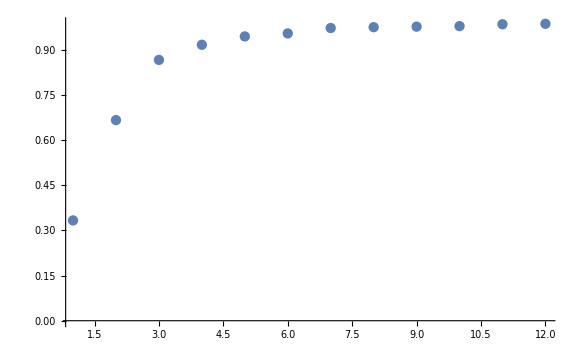

```mathematica
ListPlot[numNRTIs[[All,2]],PlotRange->All]
```

```mathematica
data=Transpose[{Range[12],numNRTIs[[All,2]]}];
```

```mathematica
logg=Fit[data,{1,Log[x],Log[x]^2},x]
```

0.333387+0.60979 Log[x]-0.142249 Log[x]^2

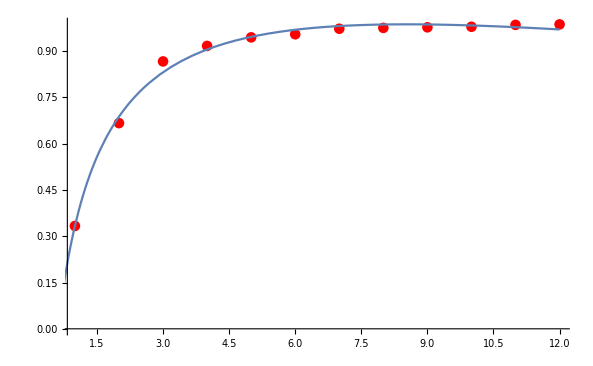

```mathematica
Show[ListPlot[data,PlotStyle->Red,PlotRange->All],Plot[{logg},{x,0,12},PlotRange->All]]
```